### Drawing edges between gaussian primes Strategy: generate a list of the Gaussian primes in the area from the x-axis to the line y = x. Because of the area we’ve limited ourselves to, we’ll only need to calculate one Gaussian prime per prime number. For each gaussian prime, determine the neighboring gaussian primes that are at most distance k away. Reflect the adjacent points across the line y = x, the x-axis and the y-axis to generate the list of all adjacent points in the graph. Draw the lines. Draw all gaussian primes. Let k be the maximum distance (or length) of an edge between 2 Gaussian points Let S be the set of all possible points of distance less than or equal to k from the origin (or norm less than or equal to k^2) in Q1 Let m be the maximum distance from the origin that we want to explore Let V be the set of Gaussian primes in Q1 between the x-axis and the line y=x of at most distance m from the origin Let L be the list of edges between g-primes of distance <= k For each member, v, of V, add v to each member, s, of S. if v+s is a g-prime, add {v, v+s} to L Reflect each member of L across y=x, then across the y=axis into Q2, then across x-axis into Q3 and Q4 Draw the lines

Let S be the set of all possible points of distance less than or equal to k from the origin (or norm less than or equal to k^2) in Q1

```mathematica
(*Assume that pt={x,y} where x ≥ y, 4 cases, x ≡ 3 mod 4, y == 0, x == y, none of previous*)
modKPoints[pt_] :=
Module[{ x = pt[[1]],y = pt[[2]]},
Which[
Mod[x, 4] == 3, (Sow[{x,0}]; Sow[{0,x}]; Sow[{0,-x}];),
y==0,(Sow[{x,y}];Sow[{y,x}];Sow[{y,-x}];),
x == y,(Sow[{x,y}];Sow[{x,-y}]), 
True, (Sow[{x,y}]Sow[{x,-y}];Sow[ {y,x}];Sow[{y,-x}];)]]

getKPoints[x_] :=
Module[
{pt = Flatten[Reverse/@PowersRepresentations[x, 2, 2], 1]},
If[Length[pt] >0, modKPoints[pt]]]

generateKPoints[maxDistance_] := Reap[Do[getKPoints[i], {i, 1, maxDistance^2}]][[2]][[1]]
```

### Let V be the set of Gaussian primes in Q1 between the x-axis and the line y=x of at most distance m from the origin

```mathematica
(*PowersRepresentation returns values in ascending order, need to reverse the values so they stay between x-axis and y=x*)
mod1Point[p_, maxXDistance_] :=
Module[{squares = Flatten[Reverse/@PowersRepresentations[p,2,2]]},
If[squares[[1]]≤ maxXDistance, Sow[squares]]]

mod3Point[p_] := Sow[{p,0}]
```

### Generate all primes up to a maximum point on the x axis. Add {1,1} to the list to make up for 2 being missed by the congruence rules

```mathematica
generatePrimePoints[maxXDistance_] := 
Union[
Reap[
Do[Which[Mod[Prime[p],4] == 1,mod1Point[Prime[p], maxXDistance], Prime[p] ≤ maxXDistance, mod3Point[Prime[p]],True, Null], {p, 2, PrimePi[2maxXDistance^2]}]][[2]][[1]], {{1,1}}]
```

### For each member, v, of V, add v to each member, s, of S. if v+s is a g-prime, add {v, v+s} to L

```mathematica
(*Add each member of s to v, return the points that are gaussian primes *)
getPrimeNeighbors[v_,sList_] := Select[Map[v+#&, sList], PrimeQ[#[[1]] + #[[2]] I ] &]

(*For each adjacent point to v that is gaussian prime, append v and the adjacent point to the line list*)
getPrimeEdges[v_, primeNeighbors_] := 
If[Length[primeNeighbors]  > 0, Sow[Map[{v,#}&,primeNeighbors]]]


(*generate the list of all edges in the graph*)
generateEdgeList[kMax_, maxDistance_] :=
Module[
{v = generatePrimePoints[maxDistance],s = generateKPoints[kMax]},
Flatten[Reap[
Do[getPrimeEdges[v[[i]], getPrimeNeighbors[v[[i]], s]], {i, 1, Length[v]}]][[2]][[1]], 1]
]
```

{{1,0},{1,0},{0,1},{0,-1},{1,1},{1,-1},{2,0},{2,0},{0,2},{0,-2}}

{{1,1},{2,1},{3,0},{3,2},{4,1},{5,2},{5,4}}

{{{1,1},{2,1}},{{1,1},{2,1}},{{1,1},{1,2}},{{1,1},{2,0}},{{1,1},{1,-1}},{{2,1},{2,0}},{{2,1},{3,2}},{{2,1},{3,0}},{{2,1},{4,1}},{{2,1},{4,1}},{{2,1},{2,3}},{{2,1},{2,-1}},{{3,0},{4,1}},{{3,0},{4,-1}},{{3,0},{5,0}},{{3,0},{5,0}},{{3,0},{3,2}},{{3,0},{3,-2}},{{3,2},{4,1}},{{3,2},{5,2}},{{3,2},{5,2}},{{3,2},{3,0}},{{4,1},{5,2}},{{4,1},{5,0}},{{4,1},{6,1}},{{4,1},{6,1}},{{4,1},{4,-1}},{{5,2},{6,1}},{{5,2},{7,2}},{{5,2},{7,2}},{{5,2},{5,4}},{{5,2},{5,0}},{{5,4},{6,5}},{{5,4},{5,6}},{{5,4},{5,2}}}

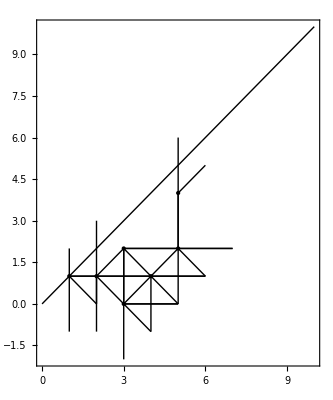

```mathematica
kMax = 2;
pt = {1,1};
s = generateKPoints[kMax]
maxDistance = 5;
v = generatePrimePoints[maxDistance]
edgeList =generateEdgeList[2, 5]

Graphics[{Line[edgeList], Point[v], Line[{{0,0}, {10,10}}]}, Frame->True, FrameTicks->Automatic]
```